Q^-1/ΔE 
d=1.7
with heat flow

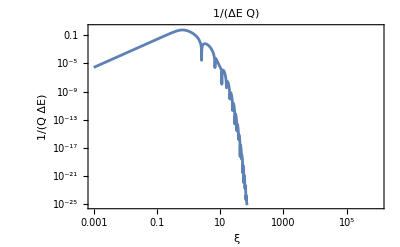

```mathematica
QHeatFlow17=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1.7};

QHeatFlowg=LogLogPlot[QHeatFlow17,{ξ,0.001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

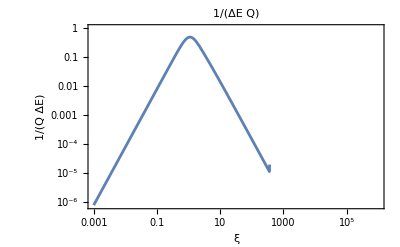

```mathematica
QHeatFlow1=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1};

QHeatFlow1g=LogLogPlot[QHeatFlow1,{ξ,0.001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

without heat flow

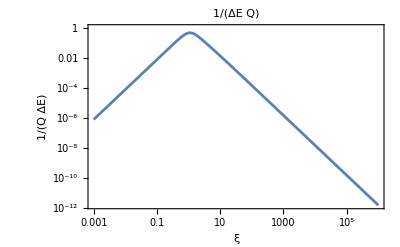

```mathematica
QNoHeatFlow =Abs[ 6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) ];

(*{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ))}/.
{ω->2π f,χ->4.47,b->2 10^-3};*)
QNoHeatFlowg=LogLogPlot[QNoHeatFlow,{ξ,0.001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

並べる

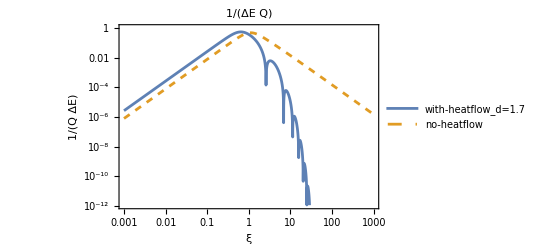

```mathematica
LogLogPlot[{QHeatFlow17,QNoHeatFlow},{ξ,0.001,1000},PlotStyle->{RightBlue,Dashed},PlotLegends->Placed[{"with-heatflow_d=1.7","no-heatflow"},{0.3,0.3}],PlotLabel->Q^-1/ΔE,Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

ディップ位置

```mathematica
FindArgMin[QHeatFlow17,{ξ,1,10}]
```

{2.5876}

```mathematica
FindArgMin[QHeatFlow17,{ξ,5,8}]
```

{6.84434}

```mathematica
FindArgMin[QHeatFlow17,{ξ,11,15}]
```

{11.2859}

```mathematica
FindArgMin[QHeatFlow17,{ξ,15,20}]
```

{15.7674}

```mathematica
FindArgMin[QHeatFlow17,{ξ,20,25}]
```

{20.2159}

```mathematica
FindArgMin[QHeatFlow17,{ξ,25,30}]
```

{24.6875}

```mathematica
FindArgMin[QHeatFlow17,{ξ,30,35}]
```

{29.1819}